```mathematica
Clear["Global`*"];
```

```mathematica
L=1;T=1.5;
Δt=0.00001;Marching=Round[T/Δt];
Period=2.1;ϵ=0.1;
ne=4;(*number of elements*)
nn=5;(*number of nodes*)
odf=9;(*open degree of freedoms*)
zz=Round[T/0.01+2];
dd=0.01/Δt;
```

```mathematica
Material Properties
Eee=2.1 10^11;(*(Kg.f)/m^2*)
ρρ=7850;(*kg/m^3*)
A1=9.1×10^-3;(*m^2 IPB220*)
Ii1=8.09×10^-5;(*m^4 IPB220*)
A2=9.1×10^-3;(*m^2 IPE240*)
Ii2=8.09×10^-5;(*m^4 IPE240*)
L1=4;
L2=5 34^0.5/5
cd=Cd=0.1;(*cdb*)
cda=0.05;
Ii={Ii1,Ii2,Ii2,Ii1};A={A1,A2,A2,A1};LLL={L1,L2,L2,L1};
```

Material Properties

5.83095

```mathematica
Ca1={√(Eee/(ρρ L1^2)),√(Eee/(ρρ L2^2)),√(Eee/(ρρ L2^2)),√(Eee/(ρρ L1^2))};Cb1={√((Eee Ii1)/(ρρ A1 L1^4)),√((Eee Ii2)/(ρρ A2 L2^4)),√((Eee Ii2)/(ρρ A2 L2^4)),√((Eee Ii1)/(ρρ A1 L1^4))};


T1=Ca1* T;
T2=Cb1* T;
Δt1=Ca1* Δt;
Δt2=Cb1 *Δt;

m11a=Table[1/8 Δt1[[i]]^4,{i,ne}];m22a=Table[1/3 Δt1[[i]]^3,{i,ne}];m33a=Table[1/2 Δt1[[i]]^2,{i,ne}];

m11b=Table[1/8 Δt2[[i]]^4,{i,ne}];m22b=Table[1/3 Δt2[[i]]^3,{i,ne}];m33b=Table[1/2 Δt2[[i]]^2,{i,ne}];
```

```mathematica
LL[x1_,y1_,x2_,y2_]:=√((x2-x1)^2+(y2-y1)^2);
θ[x1_,y1_,x2_,y2_]:=If[x2-x1==0,π/2,ArcTan[(y2-y1)/(x2-x1)]];
node={{0,0},{0,1},{5/34^0.5,1+3/34^0.5},{10/34^0.5,1},{10/34^0.5,0}};
elmn={{1,2},{2,3},{3,4},{4,5}};
x1=y1=x2=y2={};
```

```mathematica
Do[
x1=Append[x1,node_⟦elmn_⟦i,1⟧,1⟧];
y1=Append[y1,node_⟦elmn_⟦i,1⟧,2⟧];
x2=Append[x2,node_⟦elmn_⟦i,2⟧,1⟧];
y2=Append[y2,node_⟦elmn_⟦i,2⟧,2⟧],{i,1,ne}];
```

```mathematica
Le=Table[LL[x1_⟦i⟧,y1_⟦i⟧,x2_⟦i⟧,y2_⟦i⟧],{i,1,ne}];
```

```mathematica
θe=N[{Pi/2,0.5404195002705842,-0.5404195002705842,-Pi/2}];
```

```mathematica
Source Function
g1[x_]:=If[Δt-0.5≤x,0,If[-0.6≤x,-(x+(0.5-Δt))/Δt,If[-0.7≤x,-(-0.7+(0.5-Δt))/Δt+(x+(0.5-Δt))/Δt,0]]];g2[x_]:=If[x≤0.5-Δt,0,If[x≤0.6,(x-(0.5-Δt))/Δt,If[x≤0.7,(0.7-(0.5-Δt))/Δt-(x-(0.5-Δt))/Δt,0]]];
g2[x_]:=g1[-x];
```

Function Source

```mathematica
gg1[x_]:=If[0≤Abs[x]≤ϵ,-5Abs[x]+5ϵ,0];
```

```mathematica
Needs["FourierSeries`"]
SSa=13;SSb=27;
η1=L/2+0.145;
η2=L/2+0.145;
AAλ1a=AAλ2a=Table[{},{i,1,ne}];αααa=βββ1a=βββ2a=Table[{},{i,1,ne}];ba1a=ba2a=Table[{},{i,1,ne}];
Do[
Do[
AAλ1a_⟦k⟧=Append[AAλ1a_⟦k⟧,NFourierCoefficient[g1[x],x,i,FourierParameters->{1,(-2π)/Period}]];
AAλ2a_⟦k⟧=Append[AAλ2a_⟦k⟧,NFourierCoefficient[g2[x],x,i,FourierParameters->{1,(-2π)/Period}]];
αααa_⟦k⟧=Append[αααa_⟦k⟧,(-2π i ⅈ)/Period];
βββ1a_⟦k⟧=Append[βββ1a_⟦k⟧,1/Le_⟦k⟧×(-2π i ⅈ)/Period];
βββ2a_⟦k⟧=Append[βββ2a_⟦k⟧,1/Le_⟦k⟧×(2π i ⅈ)/Period];,{i,-SSa,SSa,1}];,{k,1,ne}];
```

```mathematica
AAλ1b=Table[{},{i,1,ne}];αααb=αα=zarib=Table[{},{i,1,ne}];
Do[
Do[
AAλ1b_⟦k⟧=Append[AAλ1b_⟦k⟧,Limit[Sin[π Abs[fg]/SSb]/(π Abs[fg]/SSb), fg -> i ]NFourierSinCoefficient[gg1[x-Period/2],x,i,FourierParameters->{1,-π/Period}]];
αα_⟦k⟧=Append[αα_⟦k⟧,(π i)/Period];,{i,1,SSb,1}];,{k,1,ne}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained -1.37101×10^-17 and 2.07955×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained 2.69793×10^-17 and 3.88381×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.95000038492842869558617504378633319972458082247612765058875083923}. NIntegrate obtained -1.76964×10^-17 and 5.1489×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,-αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,-AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
p1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
p2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
m1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];
m2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];,{k,1,ne}];
```

```mathematica
Do[
p1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)- (1/2(-Cd+√(Cd^2-4 α^4))) t-1)/((1/2(-Cd+√(Cd^2-4 α^4)))^2)];
p2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)- (1/2(-Cd+√(Cd^2-4 α^4))) t-1)/((1/2(-Cd+√(Cd^2-4 α^4)))^2)];

m1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)-1)/(1/2(-Cd+√(Cd^2-4 α^4)))];
m2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-Cd+√(Cd^2-4 α^4))) m22b[[k]])+cd (1/2(-Cd+√(Cd^2-4 α^4))) m33b[[k]])/((1/2(-Cd+√(Cd^2-4 α^4)))^2(α^4 m11b[[k]]+cd m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-Cd+√(Cd^2-4 α^4))) t)-1)/(1/2(-Cd+√(Cd^2-4 α^4)))];,{k,1,ne}];
```

```mathematica
Do[
Do[
If[
αααa_⟦k,i⟧≠0,
AAλ1a_⟦k,i⟧=AAλ1a_⟦k,i⟧/p1a[k,αααa_⟦k,i⟧,Δt1[[k]]];
AAλ2a_⟦k,i⟧=AAλ2a_⟦k,i⟧/p2a[k,αααa_⟦k,i⟧,Δt1[[k]]];,
ba1a_⟦k⟧=AAλ1a_⟦k,i⟧;ba2a_⟦k⟧=AAλ2a_⟦k,i⟧;];
,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
zarib1=zarib2=zarib3=zarib4=zarib;ba1b=ba2b=ba3b=ba4b=Table[{},{i,1,ne}];

Do[
Do[
zarib1_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2+η1));
zarib2_⟦k,i⟧=zarib_⟦k,i⟧/(-αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2+η2));
zarib3_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2-η1));
zarib4_⟦k,i⟧=zarib_⟦k,i⟧/(αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2-η2));,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
h0a=l0a=Table[{},{i,1,ne}];
Do[
h0a_⟦k⟧=ba1a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);l0a_⟦k⟧=ba2a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);

I1a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+h0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
I2a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]])+l0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);,{k,1,ne}];
```

```mathematica
Do[
dis2[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧);
dis4[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧);

I1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧);
I1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);I2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧)+dis2[k];
I2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧);
I3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧)+dis4[k];
I4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);,{k,1,ne}];
```

```mathematica
z1=z2=z3=z4=Table[0{k,ne},{j,4}];
Do[
z1[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{1}, {0}, {0}, {0}});z2[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {1}, {0}, {0}});z3[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {0}, {1}, {0}});z4[[k]]=Inverse[({{I1b[k,-L/2], I2b[k,-L/2], I3b[k,-L/2], I4b[k,-L/2]}, {I1bα[k,-L/2], I2bα[k,-L/2], I3bα[k,-L/2], I4bα[k,-L/2]}, {I1b[k,L/2], I2b[k,L/2], I3b[k,L/2], I4b[k,L/2]}, {I1bα[k,L/2], I2bα[k,L/2], I3bα[k,L/2], I4bα[k,L/2]}})].({{0}, {0}, {0}, {1}});
,{k,1,ne}];
```

```mathematica
ZZ1=ZZ2=ZZ3=ZZ4=Table[0,{k,ne},{j,Length[αααb[[1]]]}];
```

```mathematica
Do[
Do[
ZZ1[[k,i]]=z1[[k,1]]*zarib1_⟦k,i⟧+z1[[k,2]] zarib2_⟦k,i⟧+z1[[k,3]] zarib3_⟦k,i⟧+z1[[k,4]] zarib4_⟦k,i⟧;
ZZ2[[k,i]]=z2[[k,1]]*zarib1_⟦k,i⟧+z2[[k,2]] zarib2_⟦k,i⟧+z2[[k,3]] zarib3_⟦k,i⟧+z2[[k,4]] zarib4_⟦k,i⟧;
ZZ3[[k,i]]=z3[[k,1]]*zarib1_⟦k,i⟧+z3[[k,2]] zarib2_⟦k,i⟧+z3[[k,3]] zarib3_⟦k,i⟧+z3[[k,4]] zarib4_⟦k,i⟧;
ZZ4[[k,i]]=z4[[k,1]]*zarib1_⟦k,i⟧+z4[[k,2]] zarib2_⟦k,i⟧+z4[[k,3]] zarib3_⟦k,i⟧+z4[[k,4]] zarib4_⟦k,i⟧;
,{i,1,Length[αααb[[1]]]}];
,{k,1,ne}];
```

```mathematica
con1=con2=con3=con4=Table[0,{k,ne}];
```

```mathematica
Do[
con1[[k]]=z1[[k,1,1]]*0+z1[[k,2,1]]dis2[k]+z1[[k,3,1]]*0+z1[[k,4,1]]dis4[k];
con2[[k]]=z2[[k,1,1]]*0+z2[[k,2,1]]dis2[k]+z2[[k,3,1]]*0+z2[[k,4,1]]dis4[k];
con3[[k]]=z3[[k,1,1]]*0+z3[[k,2,1]]dis2[k]+z3[[k,3,1]]*0+z3[[k,4,1]]dis4[k];
con4[[k]]=z4[[k,1,1]]*0+z4[[k,2,1]]dis2[k]+z4[[k,3,1]]*0+z4[[k,4,1]]dis4[k];
,{k,1,ne}];
N1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con1[[k]];
N1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con2[[k]];
N2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;


N3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con3[[k]];
N3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con4[[k]];
N4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[k,i,1]](p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;
```

```mathematica
Plot[{Re[N2bααα[2,x]]},{x,-0.5,0.5},PlotPoints->3,PlotRange->All,PlotStyle->Thick]
```

842490168*^9}, {3.674973668766868*^9, 

   3.6749736918624372`*^9}, 3.674974305457653*^9, 3.6749801234004173`*^9, 

   3.6752131359051476`*^9, {3.675305515938533*^9, 3.675305521070942*^9}, {

   3.6753066558282747`*^9, 3.675306696871947*^9}, 3.675307027561328*^9, 

   3.675307345756087*^9, {3.6753086302945004`*^9, 3.675308633492506*^9}, 

   3.675309112023346*^9, 3.6753095323597355`*^9, {3.6753131069493837`*^9, 

   3.6753131073549843`*^9}, 3.6753133355687795`*^9, {3.675396068618267*^9, 

   3.6753960905595226`*^9}, {3.676093074026656*^9, 3.676093104399909*^9}, 

   3.677206190374045*^9, 3.677300619992685*^9, {3.679199422124481*^9, 

   3.67919950708223*^9}, {3.6797153514713497`*^9, 3.6797153690837803`*^9}, {

   3.6797172169536257`*^9, 3.679717235533259*^9}, {3.679723266386056*^9, 

   3.6797232717836657`*^9}, {3.6814449940567465`*^9, 

   3.6814450048363657`*^9}, {3.6814480034548187`*^9, 3.681448004274865*^9}, {

   3.6814487195407763`*^9, 3.6814487305724072`*^9}, {3.683268255654559*^9, 

   3.683268256682618*^9}, {3.6836990664388356`*^9, 3.683699066875636*^9}, 

   3.6836991231293354`*^9, {3.6836993656161613`*^9, 3.6836993659281616`*^9}, 

   3.6837049418252563`*^9, {3.6837051337991934`*^9, 3.6837051460296144`*^9}, 

   3.684398252397496*^9, {3.686718963054881*^9, 3.6867189789513083`*^9}, 

   3.6867202479511375`*^9, {3.6867273630383787`*^9, 3.6867273646295815`*^9}, 

   3.6867273950964355`*^9, 3.686730002853443*^9, 3.6867305207119527`*^9, {

   3.6870562047961473`*^9, 3.68705621060748*^9}, {3.687056465894081*^9, 

   3.687056465994087*^9}, {3.6870664513952193`*^9, 3.6870664517382393`*^9}, {

   3.702971227657358*^9, 3.7029712277663646`*^9}, {3.760423106260603*^9, 

   3.76042313691737*^9}, {3.7604238120311756`*^9, 3.760423814259761*^9}, 

   3.760423862037693*^9, {3.760423957487528*^9, 3.7604239576336317`*^9}, {

   3.760424161915577*^9, 3.760424227724413*^9}, {3.7604244941527205`*^9, 

   3.7604244967915945`*^9}, {3.76042453747751*^9, 3.7604245616336775`*^9}, {

   3.7604269126088696`*^9, 3.7604269422212915`*^9}, {3.760426993761923*^9, 

   3.760426994247286*^9}, 3.7604303934861116`*^9, 3.7604304260045824`*^9, {

   3.7604304579689484`*^9, 3.760430458316208*^9}, 3.7604308433078165`*^9, {

   3.7604309016274643`*^9, 3.7604309019566936`*^9}, {3.760431873393071*^9, 

   3.7604318739164443`*^9}, {3.7604319721746283`*^9, 3.760431973595645*^9}, {

   3.7611069928697615`*^9, 3.761107003869137*^9}, {3.7611070980060244`*^9, 

   3.761107100787997*^9}, {3.7611075208127637`*^9, 3.761107521765728*^9}, 

   3.761107614661563*^9, 3.7611163326469827`*^9, {3.7611163799894643`*^9, 

   3.761116386549387*^9}, {3.7611188310438485`*^9, 3.76111884174142*^9}, {

   3.7611252356886654`*^9, 3.761125240091784*^9}, 3.7611254197233906`*^9, {

   3.761126573439864*^9, 3.7611265769683623`*^9}, {3.761126633952259*^9, 

   3.761126634386571*^9}, 3.7611268468432426`*^9, {3.7611268965102663`*^9, 

   3.7611268993752947`*^9}, {3.761128607073822*^9, 3.7611286127078066`*^9}, {

   3.761130654214566*^9, 3.7611307381289377`*^9}, 3.761130843960514*^9, {

   3.761131396157119*^9, 3.7611314415102463`*^9}, {3.761132481727153*^9, 

   3.7611324847013483`*^9}, {3.7611338666498384`*^9, 

   3.7611338760284758`*^9}, {3.7611432074660406`*^9, 3.7611432300751796`*^9}, 

   3.761143890799944*^9, {3.7611439237540646`*^9, 3.761143933022629*^9}, {

   3.7611440226461926`*^9, 3.761144046448901*^9}, {3.76114685792651*^9, 

   3.761146866002944*^9}, 3.7611470116736574`*^9, {3.7611471613779883`*^9, 

   3.761147161528099*^9}, {3.7611473818427854`*^9, 3.7611474172498784`*^9}, {

   3.7611477064107003`*^9, 3.761147706634838*^9}, {3.761209623371669*^9, 

   3.7612096550982285`*^9}, {3.7612115091603136`*^9, 

   3.7612115157535124`*^9}, {3.761211926664139*^9, 3.7612119351625905`*^9}, {

   3.761221427202998*^9, 3.7612214296877575`*^9}, {3.7612227759723225`*^9, 

   3.761222780476512*^9}, {3.7612810529483733`*^9, 3.76128105758066*^9}, {

   3.761281274837406*^9, 3.7612812825939074`*^9}, {3.761282532249084*^9, 

   3.761282532388184*^9}, {3.7612826675125866`*^9, 3.761282674359442*^9}, {

   3.761284636495797*^9, 3.761284644091263*^9}, {3.7612887663177114`*^9, 

   3.7612887665018415`*^9}, {3.7612898534095774`*^9, 3.761289860218404*^9}, 

   3.761294972697295*^9, 3.7612953439514093`*^9, 3.7612954596990337`*^9, {

   3.761308519678688*^9, 3.761308522922001*^9}, 3.7613085630280333`*^9, {

   3.7613095521519165`*^9, 3.7613095585944805`*^9}, {3.7613097159213424`*^9, 

   3.7613097179477615`*^9}, 3.7613097729740148`*^9, 3.761361375541274*^9, {

   3.761362489296508*^9, 3.761362492258609*^9}, 3.761362555925514*^9, {

   3.761687783248*^9, 3.7616878241070004`*^9}, 3.7697805171041064`*^9, {

   3.786713014080551*^9, 3.7867130142211714`*^9}, {3.8456053848076687`*^9, 

   3.8456053921458826`*^9}, {3.845605812671002*^9, 3.8456058212007303`*^9}, {

   3.8456064344659185`*^9, 3.8456064402800426`*^9}, {3.8456072021324687`*^9, 

   3.8456072075683317`*^9}, 3.8456100933753314`*^9, {3.845610149351162*^9, 

   3.845610155728697*^9}, 3.8456115167051163`*^9, {3.8456118330799656`*^9, 

   3.8456118424264574`*^9}, 3.845612571556622*^9, {3.845612943393858*^9, 

   3.8456129463319445`*^9}, 3.8456134475057006`*^9, {3.845614089720369*^9, 

   3.845614090341816*^9}, {3.8456143458046627`*^9, 3.845614345977786*^9}, 

   3.8456144093427086`*^9, 3.8456144779769797`*^9, 3.8456145415772552`*^9, 

   3.8456146731982846`*^9, {3.845625450145166*^9, 3.8456254504889193`*^9}, {

   3.8456255017725286`*^9, 3.8456255126234226`*^9}, {3.8456256478534937`*^9, 

   3.8456256548985043`*^9}, {3.8456257116620655`*^9, 3.8456257215441027`*^9}, 

   3.845627871759012*^9, {3.8456282948741755`*^9, 3.845628295756808*^9}, {

   3.8456286837612753`*^9, 3.845628693160099*^9}, {3.845993959298458*^9, 

   3.845993967685408*^9}, 3.845994170868725*^9, 3.845995305645576*^9, {

   3.8459965378811054`*^9, 3.845996543930398*^9}, {3.846088450969735*^9, 

   3.846088454261081*^9}, {3.8460897875163155`*^9, 3.846089798078822*^9}, {

   3.846090009315891*^9, 3.8460900411941023`*^9}, 3.8460902767141013`*^9, {

   3.8460910132269917`*^9, 3.8460910138253994`*^9}, {3.851703960756707*^9, 

   3.8517039704150095`*^9}, {3.851704294779072*^9, 3.85170432226027*^9}, {

   3.8517047168764935`*^9, 3.8517047233467236`*^9}, 3.8517048228381615`*^9, {

   3.8517048993881035`*^9, 3.851704911361498*^9}, {3.851707367617463*^9, 

   3.8517073817822638`*^9}, {3.851708794497271*^9, 3.851708795872263*^9}, {

   3.8517129144529567`*^9, 3.851712935422329*^9}, 3.851917418634181*^9, 

   3.8519174828535023`*^9, {3.8519190850933094`*^9, 3.8519191048823566`*^9}, 

   3.8519212168600817`*^9, 3.853673123023425*^9, {3.853673459219813*^9, 

   3.8536734666475973`*^9}, {3.853677136367693*^9, 3.853677139102103*^9}, {

   3.8539248619244175`*^9, 3.8539248650025554`*^9}, {3.8540276467315006`*^9, 

   3.854027661659436*^9}, {3.854029090156607*^9, 3.8540290956500826`*^9}, {

   3.8540723329035525`*^9, 3.8540723349756937`*^9}, {3.854072423917837*^9, 

   3.8540724389053864`*^9}, 3.854072708061714*^9, {3.85409782372722*^9, 

   3.8540978350851946`*^9}, 3.854330021354122*^9, {3.8543639764394493`*^9, 

   3.854363984010087*^9}, 3.8543641151938815`*^9, 3.854364602345287*^9, 

   3.854364947484251*^9, {3.854365268340454*^9, 3.8543652718561234`*^9}, {

   3.8543656831570973`*^9, 3.8543656834907103`*^9}, {3.8543658498787904`*^9, 

   3.854365872098252*^9}, 3.8543764761849036`*^9, {3.85437779052971*^9, 

   3.854377793093606*^9}, 3.854378189456358*^9, {3.854379097419773*^9, 

   3.8543791021854596`*^9}, {3.854379145393538*^9, 3.8543791456279154`*^9}, 

   3.8543795594419465`*^9, 3.854380105101675*^9, {3.8543809039142814`*^9, 

   3.8543809062580605`*^9}, {3.854383467131687*^9, 3.8543834703505087`*^9}, 

   3.8543835309961157`*^9, {3.8543837091360674`*^9, 3.854383712307951*^9}, {

   3.8543846985117755`*^9, 3.8543847009024305`*^9}, 3.8543850230654907`*^9, 

   3.8543851712553854`*^9, 3.8543855969644756`*^9, {3.8543860024653864`*^9, 

   3.8543860183928814`*^9}, {3.854414257174511*^9, 3.854414266599021*^9}, 

   3.854415229241108*^9, 3.8545182815264854`*^9, 3.854523092593356*^9, {

   3.8545385376996775`*^9, 3.8545385385797367`*^9}, 3.8545388326511045`*^9, {

   3.8545396145496063`*^9, 3.8545396265361176`*^9}, {3.854766477920698*^9, 

   3.854766480676708*^9}, {3.8547666494058065`*^9, 3.8547666504144883`*^9}, {

   3.8547666900111256`*^9, 3.854766699436438*^9}, {3.8547669876254587`*^9, 

   3.8547669914692597`*^9}, 3.8547670789130983`*^9, {3.854767241243747*^9, 

   3.854767251466506*^9}, 3.8547677849360948`*^9, 3.854769509005764*^9, 

   3.854770236728821*^9, {3.8547707774097757`*^9, 3.854770792476225*^9}, {

   3.8547708823199983`*^9, 3.8547708972733135`*^9}, 3.8547903580345483`*^9, 

   3.85479058020199*^9, 3.854805935554392*^9, 3.8548086464690075`*^9, 

   3.854808980222577*^9, {3.8548096277593203`*^9, 3.8548096493767157`*^9}, 

   3.8548101137545156`*^9, 3.8548120196176624`*^9, {3.8548513740803447`*^9, 

   3.8548513817865443`*^9}, {3.8548922857499356`*^9, 3.854892286890602*^9}, {

   3.8574300306615057`*^9, 3.8574301644890914`*^9}, {3.857431293739947*^9, 

   3.857431296991132*^9}, {3.8574313749225893`*^9, 3.857431375375719*^9}, 

   3.8574314292403336`*^9, 3.85743155744441*^9, {3.8574317782000027`*^9, 

   3.857431785188857*^9}, {3.8585034095496807`*^9, 3.858503414906481*^9}, {

   3.8866620848326435`*^9, 3.8866620974305925`*^9}, {3.886662584541458*^9, 

   3.886662586072549*^9}, {3.88666309461769*^9, 3.886663095508334*^9}, 

   3.8866632409236617`*^9, {3.886663307062617*^9, 3.886663309991726*^9}, {

   3.886663362097221*^9, 3.8866633623159733`*^9}, {3.8867236970087614`*^9, 

   3.886723700684373*^9}, {3.886865137687772*^9, 3.886865138539381*^9}, {

   3.886865202766523*^9, 3.88686520292264*^9}, {3.8868661067696447`*^9, 

   3.886866108915169*^9}, {3.88686620072042*^9, 3.886866202865942*^9}, {

   3.886866249186883*^9, 3.8868662498793745`*^9}, {3.8868664400104*^9, 

   3.8868664402105417`*^9}, {3.886910076196429*^9, 3.8869100777655354`*^9}, 

   3.8869103143163643`*^9, 3.886911017041357*^9, 3.886911083269928*^9, {

   3.8869111891904345`*^9, 3.8869112382353373`*^9}, 3.8869121510133677`*^9, 

   3.886912742462655*^9, 3.886914512111761*^9, 3.8869146438849773`*^9, 

   3.886915045927886*^9, 3.8869151633397975`*^9, 3.8869158387000265`*^9, 

   3.886915984392256*^9, 3.8869162487051907`*^9, {3.886924623507509*^9, 

   3.8869246236566334`*^9}, {3.88692466901306*^9, 3.8869246700558023`*^9}, {

   3.8869425429069834`*^9, 3.886942543736579*^9}, {3.8869426446312976`*^9, 

   3.8869426469699545`*^9}, {3.8869427754907904`*^9, 3.88694277632241*^9}, {

   3.887159749999508*^9, 3.88715975357804*^9}, {3.8871670059792013`*^9, 

   3.887167009762885*^9}, {3.8875045738438435`*^9, 3.887504580604643*^9}, {

   3.887524133994035*^9, 3.887524136684416*^9}, 3.887802760636712*^9, {

   3.897004947826558*^9, 3.8970049517110615`*^9}, {3.8970050146925316`*^9, 

   3.897005052733674*^9}, {3.8970051017731037`*^9, 3.897005127159128*^9}, {

   3.897005161183772*^9, 3.897005329166891*^9}, {3.897006333531158*^9, 

   3.8970063413923016`*^9}, {3.8970088522566557`*^9, 

   3.8970088624699078`*^9}, {3.897469612118256*^9, 3.8974696154815583`*^9}, {

   3.8974701077908335`*^9, 3.897470122189243*^9}, {3.8974701998483477`*^9, 

   3.8974702000202274`*^9}, 3.897470244117649*^9, {3.897742210256114*^9, 

   3.8977422114280033`*^9}, {3.8977454893399496`*^9, 

   3.8977454942306333`*^9}, {3.897746558056391*^9, 3.8977465715096755`*^9}, {

   3.897746626532767*^9, 3.897746630209077*^9}, {3.8977469610327435`*^9, 

   3.897746996006155*^9}, {3.8977510305918193`*^9, 3.897751030956085*^9}, {

   3.8977821829140763`*^9, 3.897782192494763*^9}, {3.897782744515298*^9, 

   3.897782746867326*^9}, 3.8977925512469873`*^9, 3.8978712419977446`*^9, {

   3.897871491451373*^9, 3.8978715122599754`*^9}, {3.912497491743478*^9, 

   3.9124974920226803`*^9}, 3.912499922741597*^9, 3.912500746886772*^9, {

   3.9127646522292547`*^9, 3.9127646526595592`*^9}, 3.9127657548810225`*^9, 

   3.912766332136158*^9, 3.9127667705908937`*^9, 3.9127672891448913`*^9, 

   3.9127678159517345`*^9, {3.912768276343317*^9, 3.912768276553466*^9}, 

   3.912768606435936*^9, {3.912769280426402*^9, 3.912769281405122*^9}, {

   3.914206804136443*^9, 3.914206805575458*^9}, {3.9142069958883033`*^9, 

   3.9142069974594193`*^9}, {3.955442485970886*^9, 3.9554424860958824`*^9}, {

   3.95544258409359*^9, 3.9554425879684772`*^9}, 3.9554431786480503`*^9, {

   3.955443328411724*^9, 3.9554433286148415`*^9}, 3.9554443318866158`*^9, {

   3.9554461512439137`*^9, 3.955446151493906*^9}, {3.9555929887664776`*^9, 

   3.9555930045159893`*^9}, 3.9555930601011715`*^9, {3.9555949709069653`*^9, 

   3.955594974516241*^9}, 3.955596006335867*^9, {3.9555961186765633`*^9, 

   3.955596129238735*^9}, {3.9555983415241375`*^9, 3.955598342524105*^9}, 

   3.955598442864628*^9, 3.9555985171609745`*^9, {3.955598557547966*^9, 

   3.9555985579229527`*^9}},

 ExpressionUUID -> "3b49d4b1-b8c5-4b48-bd65-48ffdf27a1f2"],



Cell[CellGroupData[{



Cell[BoxData[{

 StyleBox[

  RowBox[{"Material", " ", "Properties"}], 

  "Subsubsection"], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"Eee", "=", 

    RowBox[{"2.1", " ", 

     SuperscriptBox["10", "11"]}]}], ";"}], 

  RowBox[{"(*", 

   FractionBox[

    RowBox[{"Kg", ".", "f"}], 

    SuperscriptBox["m", "2"]], "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"\[Rho]\[Rho]", "=", "7850"}], ";"}], 

  RowBox[{"(*", 

   FractionBox["kg", 

    SuperscriptBox["m", "3"]], "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"A1", "=", 

    RowBox[{"9.1", "\[Times]", 

     SuperscriptBox["10", 

      RowBox[{"-", "3"}]]}]}], ";"}], 

  RowBox[{"(*", 

   RowBox[{

    SuperscriptBox["m", "2"], " ", "IPB220"}], 

   "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"Ii1", "=", 

    RowBox[{"8.09", "\[Times]", 

     SuperscriptBox["10", 

      RowBox[{"-", "5"}]]}]}], ";"}], 

  RowBox[{"(*", 

   RowBox[{

    SuperscriptBox["m", "4"], " ", "IPB220"}], 

   "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"A2", "=", 

    RowBox[{"9.1", "\[Times]", 

     SuperscriptBox["10", 

      RowBox[{"-", "3"}]]}]}], ";"}], 

  RowBox[{"(*", 

   RowBox[{

    SuperscriptBox["m", "2"], " ", "IPE240"}], 

   "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{

   RowBox[{"Ii2", "=", 

    RowBox[{"8.09", "\[Times]", 

     SuperscriptBox["10", 

      RowBox[{"-", "5"}]]}]}], ";"}], 

  RowBox[{"(*", 

   RowBox[{

    SuperscriptBox["m", "4"], " ", "IPE240"}], 

   "*)"}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"L1", "=", "4"}], ";"}], "\[IndentingNewLine]", 

 RowBox[{"L2", "=", 

  RowBox[{"5", " ", 

   RowBox[{

    SuperscriptBox["34", "0.5"], "/", "5"}]}]}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"cd", "=", 

   RowBox[{"Cd", "=", "0.1"}]}], ";", 

  RowBox[{"(*", "cdb", "*)"}], "\[IndentingNewLine]", 

  RowBox[{"cda", "=", "0.05"}], ";"}], "\[IndentingNewLine]", 

 RowBox[{

  RowBox[{"Ii", "=", 

   RowBox[{"{", 

    RowBox[{"Ii1", ",", "Ii2", ",", "Ii2", ",", "Ii1"}], "}"}]}], ";", 

  RowBox[{"A", "=", 

   RowBox[{"{", 

    RowBox[{"A1", ",", "A2", ",", "A2", ",", "A1"}], "}"}]}], ";", 

  RowBox[{"LLL", "=", 

   RowBox[{"{", 

    RowBox[{"L1", ",", "L2", ",", "L2", ",", "L1"}], "}"}]}], 

  ";"}], "\[Indenting

```mathematica
S1a=S2a=Table[{},{i,1,ne}];
Do[
S1a_⟦k⟧=I1a[k,-L/2];S2a_⟦k⟧=I1a[k,L/2];
N1a[k_,x_]:=S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)I1a[k,x]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];
N2a[k_,x_]:=-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I1a[k,x]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];,{k,1,ne}];
```

```mathematica
Do[
N1αa[k_,x_]:=(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));
N2αa[k_,x_]:=(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));,{k,1,ne}];
```

```mathematica
AAa=Table[{},{i,1,ne}];
Do[Do[AAa_⟦k⟧=Append[AAa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
AAb=Table[{},{i,1,ne}];
Do[Do[AAb_⟦k⟧=Append[AAb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];
BBa=Table[{},{i,1,ne}];
Do[Do[BBa_⟦k⟧=Append[BBa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
BBb=Table[{},{i,1,ne}];
Do[Do[BBb_⟦k⟧=Append[BBb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];
```

```mathematica
disa=Table[{},{i,1,ne}];
Do[disa_⟦k⟧=0,{k,1,ne}];

dis22a=Table[{},{i,1,ne}];
Do[dis22a_⟦k⟧=0,{k,1,ne}];

disb=Table[{},{i,1,ne}];
Do[disb_⟦k⟧=0,{k,1,ne}];

dis22b=Table[{},{i,1,ne}];
Do[dis22b_⟦k⟧=0,{k,1,ne}];
```

```mathematica
k1[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{-(Eee×A[[el]])/LLL[[el]]N1αa[el,-L/2], 0, 0}, {0, Eee×Ii[[el]]×N1bααα[el,-L/2], Eee×Ii[[el]]×N2bααα[el,-L/2]}, {0, -Eee×Ii[[el]]×N1bαα[el,-L/2], -Eee×Ii[[el]]×N2bαα[el,-L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
k2[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{(Eee×A[[el]])/LLL[[el]]×N2αa[el,L/2], 0, 0}, {0, -Eee×Ii[[el]]×N3bααα[el,L/2], -Eee×Ii[[el]]×N4bααα[el,L/2]}, {0, Eee×Ii[[el]]×N3bαα[el,L/2], Eee×Ii[[el]]×N4bαα[el,L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
ke1=ke2={};
Do[AppendTo[ke1,k1[Le_⟦i⟧,θe_⟦i⟧,i]];
AppendTo[ke2,k2[Le_⟦i⟧,θe_⟦i⟧,i]];
,{i,1,ne}];
```

```mathematica
Table[MatrixForm[ke1_⟦i⟧],{i,ne}];Table[MatrixForm[ke2_⟦i⟧],{i,ne}];
MatrixForm[ke1];
```

```mathematica
t[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
B1=({{1, 2}, {2, 3}, {3, 4}, {4, 5}});
te={};
Do[AppendTo[te,t[θe_⟦i⟧]],{i,1,ne}];
Table[MatrixForm[te_⟦i⟧],{i,ne}];
MatrixForm[te[[1]]];
```

```mathematica
K=Table[0,{i,nn},{j,3},{r,3}];
For[i=1,i≤ne,i++,
For[j=1,j≤2,j++,
If[j==1,K_⟦B1_⟦i,j⟧⟧+=ke1_⟦i⟧,K_⟦B1_⟦i,j⟧⟧+=ke2_⟦i⟧];
];
];
```

```mathematica
Open degree of freedom
odf1=ReplacePart[Table[3,{i,nn}],{1->0,5->0}];
dof=Table[0,{i,nn},{j,3}];
dof=ReplacePart[dof,{{1,1}->1,{1,2}->1,{1,3}->1,{5,1}->1,{5,2}->1,{5,3}->1}];
```

degree freedom of Open

```mathematica
Assembling
K1=Kuu={};

Do[
K1=Append[K1,Table[0,{j,odf1[[i]]},{r,3}]];
Kuu=Append[Kuu,Table[0,{j,odf1[[i]]},{r,odf1[[i]]}]];
,{i,1,nn}]
```

Assembling

```mathematica
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
K1_⟦i,j,All⟧=K_⟦i,Ordering[dof[[i]]]_⟦j⟧,All⟧
];
];
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
Kuu_⟦i,All,j⟧=K1_⟦i,All,Ordering[dof[[i]]]_⟦j⟧⟧
];
];
```

```mathematica
FF={};
Do[
FF=Append[FF,If[Length[Kuu[[i]]]==0,0,Inverse[Kuu[[i]]]]];
,{i,1,nn}];
```

```mathematica
RR1=Table[0,{i,ne},{k,3},{h,1}];RR2=Table[0,{i,ne},{k,3},{h,1}];R1=Table[0,{j,6 nn},{k,1}];Ru=Table[0,{j,odf},{k,1}];ww=Table[0,{j,nn},{k,3}];wwt=Table[0,{j,6 nn},{k,1}];wwe=Table[0,{i,ne},{k,6},{h,1}];wwe1=Table[0,{i,ne},{k,3},{h,1}];wwe2=Table[0,{i,ne},{k,3},{h,1}];Δwe6=Table[0,{i,ne},{k,6},{h,1}];Δwe61=Table[0,{i,ne},{k,3},{h,1}];Δwe62=Table[0,{i,ne},{k,3},{h,1}];CC=Table[0,{i,ne},{k,4},{h,1}];wa=Table[0,{i,Marching}];
```

```mathematica
BPc={-L/2,L/2};
BPa=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααa_⟦1⟧]}];
BPb=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Do[
BPa_⟦k,q,i⟧=ⅇ^(αααa_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααa_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Do[
BPb_⟦k,q,i⟧=ⅇ^(αααb_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααb_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Ezafea=Table[{},{k,1,ne},{i,1,Length[αααa_⟦1⟧]}];
Ezafeb=Table[{},{k,1,ne},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Ezafea_⟦k,i⟧=Append[Ezafea_⟦k,i⟧,m33a[[k]]/(αααa_⟦k,i⟧^2 m11a[[k]]-cda m22a[[k]]-m33a[[k]])Δt1[[k]]^2/2];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Ezafeb_⟦k,i⟧=Append[Ezafeb_⟦k,i⟧,(αααb_⟦k,i⟧^4  m33b[[k]])/(αααb_⟦k,i⟧^4*m11b[[k]]+cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Source1a=Source2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Source1b=Source2b=Source3b=Source4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Source1a_⟦k,i⟧=Append[Source1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Source2a_⟦k,i⟧=Append[Source2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Source1b_⟦k,i⟧=Append[Source1b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1[[k,i,1]]];
Source2b_⟦k,i⟧=Append[Source2b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2[[k,i,1]]];
Source3b_⟦k,i⟧=Append[Source3b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3[[k,i,1]]];
Source4b_⟦k,i⟧=Append[Source4b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4[[k,i,1]]];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Sourcett1a=Sourcett2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Sourcett1b=Sourcett2b=Sourcett3b=Sourcett4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Sourcett1a_⟦k,i⟧=Append[Sourcett1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Sourcett2a_⟦k,i⟧=Append[Sourcett2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Sourcett1b_⟦k,i⟧=Append[Sourcett1b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1_⟦k,i,1⟧];
Sourcett2b_⟦k,i⟧=Append[Sourcett2b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2_⟦k,i,1⟧];
Sourcett3b_⟦k,i⟧=Append[Sourcett3b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3_⟦k,i,1⟧];
Sourcett4b_⟦k,i⟧=Append[Sourcett4b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4_⟦k,i,1⟧];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
P=Table[0,{i,Marching},{k,1,nn},{k,3}];
P[[1,4,1]]=1;
```

```mathematica
rr=0;
 aa=ab=Table[0,{i,ne}];
```

```mathematica
Do[
aa[[k]]=(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]+Δt1[[k]]^2/2)/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
ab[[k]]=(-(Cd m11b[[k]]+m22b[[k]])/(Cd m22b[[k]]+m33b[[k]])Δt2[[k]]^1/1+Δt2[[k]]^2/2)/(-(Cd m11b[[k]]+m22b[[k]])/(Cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2+Δt2[[k]]^3/6);,{k,1,ne}];
```

```mathematica
www={};
Do[
www=Append[www,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];
```

```mathematica
Main Program
Do[
COa=AAa(1-Ezafea αααa^2)+BBa(Δt1-Ezafea×((αααa^2 m22a)/m33a-cda));
COαa=αααa×COa;
COb=AAb(1-Ezafeb)+BBb(Δt2-Ezafeb×((m22b)/m33b+cd/αααb^4));
COαb=αααb×COb;
COααb=(αααb)^2×COb;
COαααb=(αααb)^3×COb;


f=fα=Table[{},{i,1,6}];
f1=fα1=Table[{},{i,1,3}];f2=fα2=Table[{},{i,1,3}];


Do[
f1_⟦1⟧=Append[f1_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]+dis22a_⟦k⟧(Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f1_⟦2⟧=Append[f1_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cd m33b[[k]] dis22b_⟦k⟧)/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f1_⟦3⟧=Append[f1_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];


f2_⟦1⟧=Append[f2_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f2_⟦2⟧=Append[f2_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cd m33b[[k]] dis22b_⟦k⟧)/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f2_⟦3⟧=Append[f2_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];

,{k,1,ne}];

Do[
fα1_⟦1⟧=Append[fα1_⟦1⟧,-(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]];
fα1_⟦2⟧=Append[fα1_⟦2⟧,(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];
fα1_⟦3⟧=Append[fα1_⟦3⟧,-(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];

fα2_⟦1⟧=Append[fα2_⟦1⟧,(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]];
fα2_⟦2⟧=Append[fα2_⟦2⟧,-(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];
fα2_⟦3⟧=Append[fα2_⟦3⟧,(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];

,{k,1,ne}];
Do[
RR1_⟦k⟧=(ke1_⟦k⟧.(Transpose[te_⟦k⟧].f1_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα1_⟦All,k⟧);
RR2_⟦k⟧=(ke2_⟦k⟧.(Transpose[te_⟦k⟧].f2_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα2_⟦All,k⟧);
,{k,1,ne}];
RR=Table[0,{i,nn},{k,3},{h,1}];
For[i=1,i≤ne,i++,
For[r=1,r≤2,r++,
If[r==1,RR_⟦B1_⟦i,r⟧⟧+=RR1_⟦i⟧,RR_⟦B1_⟦i,r⟧⟧+=RR2_⟦i⟧];
];
];


Ru={};
Do[
Ru=Append[Ru,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];


For[i=1,i≤nn,i++,
For[r=1,r≤odf1[[i]],r++,
Ru_⟦i,r⟧=RR_⟦i,Ordering[dof[[i]]]_⟦r⟧⟧
];
];



Do[
If[Length[FF[[i]]]≠0,www[[i]]=FF[[i]].(Ru[[i]]+P[[j,i]])];
,{i,1,nn}];


For[i=1,i≤nn,i++,
For[r=1,r≤3,r++,
If[dof_⟦i,r⟧≠1,ww_⟦i,r⟧=Flatten[www_⟦i,r⟧][[1]];
];
];
];

For[ele=1,ele≤ne,ele++,
For[r=1,r≤3,r++,
wwe1_⟦ele,r⟧=ww_⟦B1_⟦ele,1⟧,r⟧;
wwe2_⟦ele,r⟧=ww_⟦B1_⟦ele,2⟧,r⟧;
];
];


Do[
Δwe61_⟦i⟧=te_⟦i⟧.(Flatten[(wwe1_⟦i⟧)-(Transpose[te_⟦i⟧].f1_⟦All,i⟧)]);
Δwe62_⟦i⟧=te_⟦i⟧.(Flatten[(wwe2_⟦i⟧)-(Transpose[te_⟦i⟧].f2_⟦All,i⟧)]);
,{i,1,ne}];

wa[[j]]=Re[ww[[2,1]]];

If[j≠Marching,
BBa=BBa×(1-Ezafea ((αααa^2 m22a)/m33a -cda)2/Δt1)-AAa×Ezafea αααa^2×2/Δt1+Sourcett1a×Δwe61_⟦;;,1⟧+Sourcett2a×Δwe62_⟦;;,1⟧;


BBb=BBb×(1-Ezafeb(m22b/m33b+cd/αααb^4)2/Δt2)-AAb×Ezafeb×2/Δt2+
Sourcett1b×Δwe61_⟦;;,2⟧+Sourcett2b×Δwe61_⟦;;,3⟧+Sourcett3b×Δwe62_⟦;;,2⟧+Sourcett4b×Δwe62_⟦;;,3⟧;


AAa=COa+Source1a×Δwe61_⟦;;,1⟧+Source2a×Δwe62_⟦;;,1⟧;

AAb=COb+Source1b×Δwe61_⟦;;,2⟧+Source2b×Δwe61_⟦;;,3⟧+Source3b×Δwe62_⟦;;,2⟧+Source4b×Δwe62_⟦;;,3⟧;

Do[
disa_⟦k⟧=disa_⟦k⟧+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]]) Δt1[[k]]^2/2)+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe62_⟦k,1⟧;

dis22a_⟦k⟧=dis22a_⟦k⟧ (1-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]])+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧) (aa[[k]])Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)(aa[[k]])Δwe62_⟦k,1⟧;

disb_⟦k⟧=disb_⟦k⟧+dis22b_⟦k⟧ (Δt2[[k]]-(cd m33b[[k]])/(cd m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2)+con1[[k]]×Δwe61_⟦k,2⟧+con2[[k]]×Δwe61_⟦k,3⟧+con3[[k]]×Δwe62_⟦k,2⟧+con4[[k]]×Δwe62_⟦k,3⟧;


dis22b_⟦k⟧=dis22b_⟦k⟧(1-(cd m33b[[k]])/(cd m22b[[k]]+m33b[[k]])Δt2[[k]])+(con1[[k]]×Δwe61_⟦k,2⟧+con2[[k]]×Δwe61_⟦k,3⟧+con3[[k]]×Δwe62_⟦k,2⟧+con4[[k]]×Δwe62_⟦k,3⟧)ab[[k]];
,{k,1,ne}];

];
,{j,1,Marching}];
```

Main Program

Result

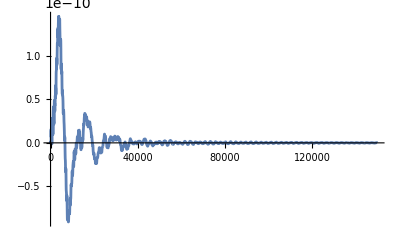

```mathematica
Result
ListPlot[wa,PlotRange->All,Joined->True]
```

```mathematica
wwa=Table[0,{i,1,Marching/100}];
Do[
wwa[[i]]=wa[[100i]];,{i,1,Marching/100}];
```

```mathematica
HH=Table[0,{i,Marching/100},{j,Marching/100}];
```

```mathematica
Do[
Do[
HH[[i+j-1,j]]=Re[wa_⟦100(i-1)+1⟧];,{i,1,Marching/100-j+1}];,{j,1,Marching/100}];
```

```mathematica
uz=Transpose[Import["C:\\Users\\Civil-Drboroumand1\\Desktop\\Ex4\\Ex4-uB.xlsx"]];(*Please,insert the storage path for the horizontal displacement response of node B.*)
```

```mathematica
ee=0.00;
```

```mathematica
DD={};
Do[
DD=Append[DD,(1+ee RandomReal[{-1,1}]) uz[[100i,1]][[1]]];,{i,1,Marching/100}];
```

```mathematica
pp=PseudoInverse[Transpose[HH].HH ].Transpose[HH].DD;
```

```mathematica
nemo1=Table[{100j Δt,pp[[j]]/100},{j,1,Marching/100,5}];
```

```mathematica
nemo2=Table[{100j Δt,If[100j Δt<1.2,1000Sin[500Pi j Δt],0]},{j,1,Marching/100}];
```

```mathematica
ListPlot[{nemo1,nemo2},Joined->True,PlotRange->All]
```

```mathematica
NN=Marching/100;
DD=Table[0,{i,NN}];
ee=0.01;
Do[
DD[[i]]= uz[[100i,1]][[1]] (1+ee RandomReal[{-1,1}]);
,{i,1,NN}];
```

```mathematica
ListPlot[DD,Joined->True]
```

```mathematica
Ee=Table[0,{i,NN},{j,NN}];
Do[
Do[
Ee[[i,j]]=ⅇ^((2 Pi ⅈ)/NN j (i-1));,{i,1,NN}];,{j,1,NN}];
```

```mathematica
Yk=DD.Ee;
ListPlot[Re[Yk],Joined->True,PlotRange->All]
```

```mathematica
Ykj=Table[0,{i,NN}];
Do[
If[Abs[Re[Yk[[i]]]]≥0.002,Ykj[[i]]=Yk[[i]]/NN;];,{i,1,NN}];
```

```mathematica
Xj=Ykj.Transpose[Ee];
```

```mathematica
ListPlot[Re[Xj],Joined->True,PlotRange->All]
```

```mathematica
XXj=Table[Xj[[NN-i+1]],{i,1,NN}];
```

```mathematica
pp=PseudoInverse[Transpose[HH].HH ].Transpose[HH].DD;
pp1=PseudoInverse[Transpose[HH].HH ].Transpose[HH].XXj;
```

```mathematica
nemo1=Table[{100j Δt,Re[pp[[j]]/100]},{j,1,Marching/100,5}];nemo11=Table[{100j Δt,Re[pp1[[j]]/100]},{j,1,Marching/100,5}];
```

```mathematica
aa1=ListPlot[{nemo1,nemo2},Joined->True,PlotRange->All]
aa2=ListPlot[{nemo11,nemo2},Joined->True,PlotRange->All]
```